This notebook was used for computations in the paper “Anti-synchrony subspaces of weighted networks” by Niholt, Sieben and Swift.

This notebook allows you to define a square matrix A, and compute the A-invariant polydiagonal subspaces.
The containment of subspaces is also computed, and a Hasse diagram of the lattice is drawn.

To run, select All and then press Shift-Enter.  This defines the functions, and also runs the examples that are there.
Define a square matrix A and then run computeLattice[A] in a new cell.  You don’t have to call the matrix A.

Implementation notes:
The polydiagonal subspaces are described in terms of color vectors.  They are integer equivalents of the typical elements used in our paper.  
There is a bijection among allowed typical elements,  allowed color vectors, and polydiagonal subspaces. For example, 
(a, b,-a, 0, c) ⟷ (1, 2, -1, 0, 3) ⟷ {(a,b,-a,0,c) ϵ R^5: a,b,c  ϵ R }.
The rules for allowed color vectors are simple: 
*No component c > 1 is allowed unless c-1 is present.  
*No component -c < 0 is allowed unless c is present.
All of the allowed color vectors of a given length n are made recursively, starting with { } of length 0, followed by {0} and {1} of length 1, etc.  This is implemented with daughterVectors[colorVector_] and makeAllColorVectors[n_].

Note that you will get a warning message when you run this notebook.
General::compat: "Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details."
This message appears in the documentation:
As of Version 10, most of the functionality of the Combinatorica package is built into the Wolfram System.
----
Most, but not all of the functionality.  Evidently the equivalent of HasseDiagram[g] is no longer available without loading Combinatorica.

Warning: The Hasse diagrams are sometimes misleading because the arrows can lie on top of each other. This happens in the computation (shown below) for Example 5.6.

Warning:  The Hasse diagrams drawn by this notebook have the trivial subspace at the bottom.  In our paper we put the trivial subspace at the top.
  
The computation computeLattice[A] takes less than a second if A is a 6x6 matrix.
The computation computeLattice[A] takes a few seconds if A is a 7x7 matrix.
The computation computeLattice[A] takes about a minute if A is an 8x8 matrix.
I don’t have the patience to run a 9x9 matrix.

```mathematica
daughterVectors[colorVector_] := Module[{dim, newComp},
If[Length[colorVector] == 0, dim= 0, (*else*)
dim = Max[colorVector] ];
(*Print[dim];*)
newComp = Range[-dim, dim+1];
(*Print[newComp];*)
Table[Append[colorVector, newComp[[i]] ], {i, 2dim+2}]
]
```

```mathematica
makeAllColorVectors[n_]:= Module[{},
list = {{}}; 
Do[
newList = {};
Do[oldVec = list[[i]] ; (*Print[oldVec];*)
newList = Join[newList, daughterVectors[oldVec] ],{i, Length[list]} ];
list = newList;
, n];
(*list = Sort[list, Sum@Abs];*)
SortBy[list, Max]];
TableForm[makeAllColorVectors[3],TableHeadings->{Automatic, None}]
```

1 | 0 | 0 | 0
2 | 0 | 0 | 1
3 | 0 | 1 | -1
4 | 0 | 1 | 0
5 | 0 | 1 | 1
6 | 1 | -1 | -1
7 | 1 | -1 | 0
8 | 1 | -1 | 1
9 | 1 | 0 | -1
10 | 1 | 0 | 0
11 | 1 | 0 | 1
12 | 1 | 1 | -1
13 | 1 | 1 | 0
14 | 1 | 1 | 1
15 | 0 | 1 | 2
16 | 1 | -1 | 2
17 | 1 | 0 | 2
18 | 1 | 1 | 2
19 | 1 | 2 | -2
20 | 1 | 2 | -1
21 | 1 | 2 | 0
22 | 1 | 2 | 1
23 | 1 | 2 | 2
24 | 1 | 2 | 3

The previous output is used to find Figure 3, which lists the polydiagonal subspaces of R^3.

This next cell checks the computation by counting p_n, the number of polydiagonal subspaces of R^n.  It will run to find p_8 in about a minute, but I don’t think it can find p_9.

```mathematica
TableForm[Table[{n,Length[makeAllColorVectors[n]]}, {n, 1, 7}], TableHeadings ->{None, {"n", "p_n"}} ]
```

n | p_n
1 | 2
2 | 6
3 | 24
4 | 116
5 | 648
6 | 4088
7 | 28640

The next cell defines a function that prints the eigenvalues and eigenvectors of a square matrix.  It lists all of the eigenvalues. It only lists eigenvectors, not generalized eigenvectors.  If the geometric multiplicity of an eigenvalue is smaller than the algebraic multiplicity, then in prints a 0 vector below the repeated eigenvalue.

```mathematica
printEigensystem[mat_] := Module[{system},
{evals, evecs} = Eigensystem[mat];(* evecs is a list of evecs as row vectors*)
components = Table["v_"<>ToString[i], {i, 1, Length[evals]}];
Print["Eigenvalues on top, eigenvectors below"];
Print@TableForm[Transpose[evecs], TableHeadings -> {None, evals}]
]
A = {{0,0,1},{1, 0,0},{0,1,0}};
Print["A = ", MatrixForm[A] ];
printEigensystem[A]
A = {{2,1,0},{0, 2,0},{0,0,2}};
Print["A = ", MatrixForm[A] ];
printEigensystem[A]
```

A = (0 | 0 | 1
1 | 0 | 0
0 | 1 | 0)

Eigenvalues on top, eigenvectors below

1 | 1/2 (-1+ⅈ √3) | 1/2 (-1-ⅈ √3)
1 | 1/2 (-1-ⅈ √3) | 1/2 (-1+ⅈ √3)
1 | 1/2 (-1+ⅈ √3) | 1/2 (-1-ⅈ √3)
1 | 1 | 1

A = (2 | 1 | 0
0 | 2 | 0
0 | 0 | 2)

Eigenvalues on top, eigenvectors below

2 | 2 | 2
0 | 1 | 0
0 | 0 | 0
1 | 0 | 0

Note: the matrix of the following form has three eigenvalues equally spaced on a circle in the complex plane centered at zero.  If a, b, an c are all real, then the lam = (abc)^(1/3) is a real eigenvalue (with lam > 0 if abc > 0 and lam < 0 if abc < 0).

```mathematica
A = {{0,0,a},{b, 0,0},{0,c,0}};
printEigensystem[A]
```

Eigenvalues on top, eigenvectors below

a^(1/3) b^(1/3) c^(1/3) | -(-1)^(1/3) a^(1/3) b^(1/3) c^(1/3) | (-1)^(2/3) a^(1/3) b^(1/3) c^(1/3)
a^(2/3)/(b^(1/3) c^(1/3)) | ((-1)^(2/3) a^(2/3))/(b^(1/3) c^(1/3)) | -((-1)^(1/3) a^(2/3))/(b^(1/3) c^(1/3))
(a^(1/3) b^(1/3))/c^(2/3) | -((-1)^(1/3) a^(1/3) b^(1/3))/c^(2/3) | ((-1)^(2/3) a^(1/3) b^(1/3))/c^(2/3)
1 | 1 | 1

```mathematica
printBothEigensystems[mat_] := Module[{evecsA, evalsA, evecsAT, evalsAT},
{evalsA, evecsA} = Eigensystem[mat];(* evecs is a list of evecs as row vectors*)
{evalsAT, evecsAT} = Eigensystem@Transpose[mat];
evals = Join[evalsA, {" "}, evalsAT];
placeHolderVector = Table[" ", {Length[mat]}];
evecs = Join[evecsA, {placeHolderVector},evecsAT];
Print["Evals on top, evecs of matrix on left, evecs of its transpose on right."];
Print@TableForm[Transpose[evecs], TableHeadings -> {None, evals}]
]
A = {{2,1,0},{0, 2,0},{0,0,2}};
Print["A = ", MatrixForm[A], ", A^T = ", MatrixForm@Transpose[A] ];
printBothEigensystems[A]
```

A = (2 | 1 | 0
0 | 2 | 0
0 | 0 | 2), A^T = (2 | 0 | 0
1 | 2 | 0
0 | 0 | 2)

Evals on top, evecs of matrix on left, evecs of its transpose on right.

2 | 2 | 2 |   | 2 | 2 | 2
0 | 1 | 0 |   | 0 | 0 | 0
0 | 0 | 0 |   | 0 | 1 | 0
1 | 0 | 0 |   | 1 | 0 | 0

```mathematica
BasisMatrixFromColorVector[colorVector_] := Module[{n = Length[colorVector], r = Max[colorVector], B, row, col},
(* The output is an n x n matrix in reduced row echelon form with rank r *)
B = Table[0,{n},{n}];
Do[
Do[
If[colorVector[[col]] == row, B[[row, col]] = 1];
If[colorVector[[col]] == -row, B[[row, col]] = -1]
, {col, 1, n}]
,{row, 1, r}];
B
]
ColorVectorFromBasisMatrix[Bmat_] := Module[{n = Length[Bmat]},
Range[Length[cvec]].Bmat
];

cvec = {1,1,2, -1, 3};
Bmat = BasisMatrixFromColorVector[cvec] ;
newCvec = ColorVectorFromBasisMatrix[Bmat];  (* This should be the original *)
Print["The color vector ", cvec, " maps to ", MatrixForm[Bmat]];
Print["That matrix maps to the color vector ", newCvec];
Print["cev = newCvec is ", cvec == newCvec];
```

The color vector {1,1,2,-1,3} maps to (1 | 1 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

That matrix maps to the color vector {1,1,2,-1,3}

cev = newCvec is True

The basis matrix returned is in reduced row echelon form, and the entries are in the set {-1,0,1}.  The polydiagonal subspace is the row space of the basis matrix.

The next cell defines some functions needed to compute and display the lattice of A-invariant polydiagonal subspaces.  It uses the Combinatorica package that is no longer supported, and most of the commands the package defines are now standard functions in Mathematica.  “Most,” but not what we need.

```mathematica
Needs["Combinatorica`"];
containment2Hasse[cont_]:=Module[{n,i,j,g,h,Adm},
n=Length[cont];
Adm=Table[Table[0,{i,1,n}],{j,1,n}];
AdmR=Table[Table[0,{i,1,n}],{j,1,n}];
For [i=1,i≤n,i=i+1,
For [j=1,j≤Length[cont[[i]]],j=j+1,
Adm[[i]][[cont[[i]][[j]]]]=1; 
]
];
(*Print[TableForm[Adm]];*)
g=FromAdjacencyMatrix[Adm,Type->Directed];
(*Print["g = ",g];*)
     (* h=HasseDiagram[SetVertexLabels[g,CharacterRange["1","z"]]]; *)
 h=HasseDiagram[ SetVertexLabels[g,Table[i,{i,1,n}]]];
g2=FromAdjacencyMatrix[Transpose[Adm],Type->Directed];
(*Print["g2 = ", g2];*)(* Printing both confirned that g and g2 are the same digraph *)
(* h2=HasseDiagram[ SetVertexLabels[g2,Table[i,{i,1,n}]]];*)
(*GraphicsRow[ {ShowGraph[h], ShowGraph[h2]}];*)
ShowGraph[h]
]
```

The next cell tests every polydiagonal subspace for A-invariance by computing the basis matrix B, and then checking if the rank of B is equal to the rank of the augmented matrix B:A.B.  It does this by checking if
reduced row echelon form of the augmented matrix B:0 is equal to the reduced row echelon form of the augmented matrix B:A.B.

```mathematica
computeLattice[A_] := (* This uses lots of RowReduce[ ] *)Module[{n = Length[A], allColorVectors (*list of all lenght n color Vectors*), genB (*list of all nxn generating matrices*), At = Transpose[A], zeroMat, AinvariantSubs, genBi, AtgenBi,genBiZeros,colorVectors,containmentList,subi,leqList,subj,ranjk,rankij,rankj},
zeroMat = Table[0,{n}, {n}];
Print["Compute ",MatrixForm[A], "-invariant polydiagonal subspaces."];
allColorVectors = makeAllColorVectors[n];
genB = Table[BasisMatrixFromColorVector[allColorVectors[[i]] ], {i, 1, Length[allColorVectors]}];
AinvariantSubs = {};
Do[genBi = genB[[i]]; genBiZeros = Join[genBi, zeroMat];
AtgenBi = Join[genBi, genBi.At];
If[genBiZeros == RowReduce[AtgenBi],(* Print@MatrixForm[genBi]; *)AppendTo[AinvariantSubs, genBi]], {i, 1, Length[genB] }];
Print["The color vectors of the invariant polydiagonal subspaces are "];
colorVectors = {};
Do[AppendTo[colorVectors,Range[n].AinvariantSubs[[i]] ], {i, Length[AinvariantSubs]}];
Print@TableForm[colorVectors, TableHeadings->{Automatic,None}];
containmentList = {};
Do[subi = AinvariantSubs[[i]];leqList ={i}; (*every subspace is less than or equal itself *)
(* We know that rank of subi = dim(Wi) ≤ rank of subj = dim(Wj)*)
Do[subj = AinvariantSubs[[j]];
rankj =MatrixRank[subj];
rankij = MatrixRank@Join[subi, subj];If[rankj == rankij, AppendTo[leqList, j]], {j, i+1, Length[AinvariantSubs]}];
AppendTo[containmentList,leqList],{i, Length[AinvariantSubs]}];
Print["The ordering of subspaces W<=V iff W subseteq V is "];
Print@TableForm[containmentList];
containment2Hasse[containmentList]
]
```

Now I will make the Hasse diagrams for the paper “Anti-synchrony subspaces of weighted networks” by Niholt, Sieben and Swift.

Compute (1 | 0
0 | 1)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0
2 | 0 | 1
3 | 1 | -1
4 | 1 | 0
5 | 1 | 1
6 | 1 | 2

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6
2 | 6 |  |  |  | 
3 | 6 |  |  |  | 
4 | 6 |  |  |  | 
5 | 6 |  |  |  | 
6 |  |  |  |  |

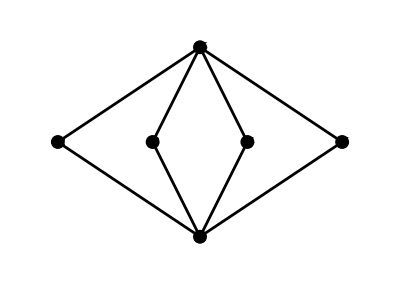

```mathematica
(* Figure 2*)
A = {{1,0}, {0,1}};
computeLattice[A]
```

Compute (0 | 0
kappa | kappa)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0
2 | 0 | 1
3 | 1 | -1
4 | 1 | 2

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4
2 | 4 |  | 
3 | 4 |  | 
4 |  |  |

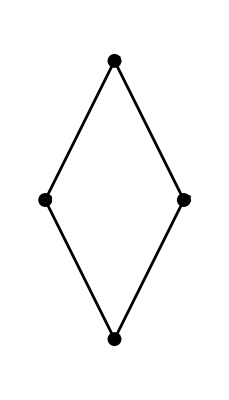

Compute (0 | 0
-kappa | kappa)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0
2 | 0 | 1
3 | 1 | 1
4 | 1 | 2

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4
2 | 4 |  | 
3 | 4 |  | 
4 |  |  |

-Graphics-

```mathematica
(* Example 4.6 *)
A = {{0,0},{kappa, kappa}};
computeLattice[A]
L = {{0,0},{-kappa, kappa}};
computeLattice[L]
```

```mathematica
(* Example 4.11 *)
L = {{1, -1},{-1,1}};
computeLattice[L]
```

Compute (1 | -1
-1 | 1)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0
2 | 1 | -1
3 | 1 | 1
4 | 1 | 2

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4
2 | 4 |  | 
3 | 4 |  | 
4 |  |  |

-Graphics-

Compute (3 | -1 | 0
-1 | 2 | -1
0 | -1 | 3)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 1 | -1 | 1
3 | 1 | 0 | -1
4 | 1 | 2 | 1
5 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5
2 | 4 | 5 |  | 
3 | 5 |  |  | 
4 | 5 |  |  | 
5 |  |  |  |

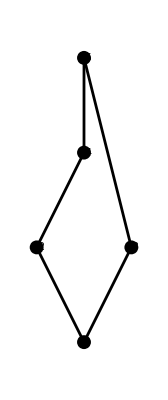

```mathematica
(* Example 5.3 *)
A = {{3, -1, 0},{-1,2,-1},{0, -1, 3}};
computeLattice[A]
```

Evals on top, evecs of matrix on left, evecs of its transpose on right.

1 | 0 | 0 |   | 1 | 0 | 0
1 | 0 | 0 |   | 1 | -1 | 0
1 | 0 | 0 |   | 0 | 1 | 0
1 | 1 | 0 |   | 0 | 0 | 0

Compute (1 | 0 | 0
1 | 0 | 0
0 | 1 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 0 | 0 | 1
3 | 1 | 1 | 1
4 | 0 | 1 | 2
5 | 1 | 1 | 2
6 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6
2 | 4 | 5 | 6 |  | 
3 | 5 | 6 |  |  | 
4 | 6 |  |  |  | 
5 | 6 |  |  |  | 
6 |  |  |  |  |

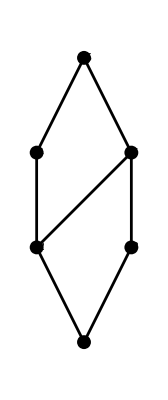

```mathematica
(* Example 5.4*)
A = {{1,0,0}, {1,0,0}, {0,1,0}};
printBothEigensystems[A]
computeLattice[A]
```

Compute (0 | 2 | 0
1 | 0 | 1
0 | 2 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 1 | -1 | 1
3 | 1 | 0 | -1
4 | 1 | 1 | 1
5 | 1 | 2 | 1
6 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6
2 | 5 | 6 |  |  | 
3 | 6 |  |  |  | 
4 | 5 | 6 |  |  | 
5 | 6 |  |  |  | 
6 |  |  |  |  |

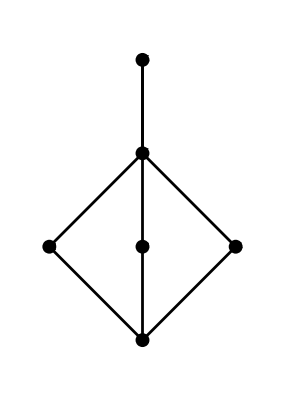

```mathematica
(* Example 5.6 *)
A = {{0,2,0},{1,0,1},{0,2,0}};
computeLattice[A]
```

The previous figure is an example of the bug in the HasseDiagram[ ] function.  (Recall that we are using a function that is no longer supported by Wolfram, and that has no equivalent in the current Mathematica language as far as I know.)
There is no arrow from 3 to 5.  There is an arrow from 3 to 6, and from 5 to 6.  These arrows are on top of each other so it looks like there is an arrow from 3 to 5.

Compute (0 | 0 | 1
1 | 0 | 0
0 | 1 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 1 | 1 | 1
3 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3
2 | 3 | 
3 |  |

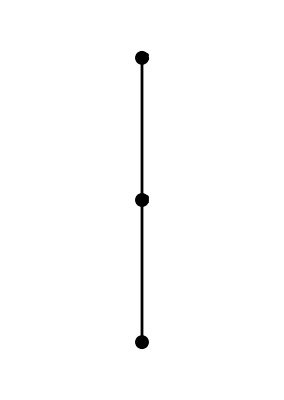

```mathematica
(* Example 6.6 *)
A = {{0,0,1},{1,0,0},{0,1,0}};
computeLattice[A]
```

```mathematica
(* Example 6.7 *)
A = {{0,1,1},{2,0,2},{1,2,0}};
printEigensystem[A]
computeLattice[A]
```

Eigenvalues on top, eigenvectors below

3 | -2 | -1
5 | 0 | -1
8 | -1 | 0
7 | 1 | 1

Compute (0 | 1 | 1
2 | 0 | 2
1 | 2 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 0 | 1 | -1
3 | 1 | 0 | -1
4 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4
2 | 4 |  | 
3 | 4 |  | 
4 |  |  |

-Graphics-

Compute (2 | 0 | -2
-1 | 1 | 0
-1 | -1 | 2)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 1 | -1 | 0
3 | 1 | 1 | 1
4 | 1 | 2 | 2
5 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5
2 | 5 |  |  | 
3 | 4 | 5 |  | 
4 | 5 |  |  | 
5 |  |  |  |

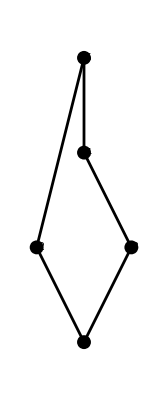

```mathematica
(* Example 6.11 *)
L = {{2,0,-2},{-1,1,0},{-1,-1,2}};
computeLattice[L]
```

```mathematica
(* Example 6.5 *)
A = {{0,t,0,0,0,0,s},{s,0,t,0,0,0,0},{0,s,0,t,0,0,0},{0,0,s,0,t,0,0},{0,0,0,s,0,t,0},{0,0,0,0,s,0,t},{t,0,0,0,0,s,0}};
MatrixForm[A]
(*
Print["Left figure, with s != t"];
computeLattice[A/.{s ->1, t->2}]
Print["Right figure, with s = t"];
computeLattice[A/.{s ->1, t->1}]
*)
```

(0 | t | 0 | 0 | 0 | 0 | s
s | 0 | t | 0 | 0 | 0 | 0
0 | s | 0 | t | 0 | 0 | 0
0 | 0 | s | 0 | t | 0 | 0
0 | 0 | 0 | s | 0 | t | 0
0 | 0 | 0 | 0 | s | 0 | t
t | 0 | 0 | 0 | 0 | s | 0)

The outputs are saved, and the commands are commented out, since this calculation takes a few seconds to compute for this 7x7 matrix.  With an 8x8 matrix, the comes back in a few minutes, but a 9x9 matrix is too large to run with this code.

(0 | t | 0 | 0 | 0 | 0 | s
s | 0 | t | 0 | 0 | 0 | 0
0 | s | 0 | t | 0 | 0 | 0
0 | 0 | s | 0 | t | 0 | 0
0 | 0 | 0 | s | 0 | t | 0
0 | 0 | 0 | 0 | s | 0 | t
t | 0 | 0 | 0 | 0 | s | 0)

Left figure, with s != t

Compute (0 | 2 | 0 | 0 | 0 | 0 | 1
1 | 0 | 2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 0 | 1 | 0 | 2
2 | 0 | 0 | 0 | 0 | 1 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 1 | 2 | 3 | 4 | 5 | 6 | 7

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3
2 | 3 | 
3 |  |

-Graphics-

Right figure, with s = t

Compute (0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 0 | 1 | 2 | 3 | -3 | -2 | -1
4 | 1 | -1 | 2 | 3 | 0 | -3 | -2
5 | 1 | 0 | -1 | 2 | 3 | -3 | -2
6 | 1 | 2 | -2 | -1 | 3 | 0 | -3
7 | 1 | 2 | 0 | -2 | -1 | 3 | -3
8 | 1 | 2 | 3 | -3 | -2 | -1 | 0
9 | 1 | 2 | 3 | 0 | -3 | -2 | -1
10 | 1 | 1 | 2 | 3 | 4 | 3 | 2
11 | 1 | 2 | 1 | 3 | 4 | 4 | 3
12 | 1 | 2 | 2 | 1 | 3 | 4 | 3
13 | 1 | 2 | 3 | 2 | 1 | 4 | 4
14 | 1 | 2 | 3 | 3 | 2 | 1 | 4
15 | 1 | 2 | 3 | 4 | 3 | 2 | 1
16 | 1 | 2 | 3 | 4 | 4 | 3 | 2
17 | 1 | 2 | 3 | 4 | 5 | 6 | 7

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
2 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 |  |  |  |  |  |  |  | 
3 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
11 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
14 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
15 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
16 | 17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

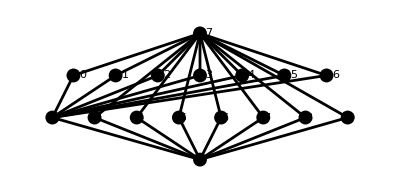

One equivalence class is {3, 4, 5, 6, 7, 8, 9}, with 3-dimensional invariant subspaces.
Another equivalence class is {10, 11, 12, 13, 14, 15, 16}, with 4-dimensional invariant subspaces.

(0 | s | 0 | 0 | 0 | t
s | 0 | t | 0 | 0 | 0
0 | t | 0 | s | 0 | 0
0 | 0 | s | 0 | t | 0
0 | 0 | 0 | t | 0 | s
t | 0 | 0 | 0 | s | 0)

Compute (0 | 1 | 0 | 0 | 0 | 2
1 | 0 | 2 | 0 | 0 | 0
0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 2 | 0 | 1
2 | 0 | 0 | 0 | 1 | 0)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | -1 | 1 | -1 | 1 | -1
3 | 1 | 1 | 1 | 1 | 1 | 1
4 | 1 | 2 | 1 | 2 | 1 | 2
5 | 1 | -1 | 2 | 3 | -3 | -2
6 | 1 | 1 | 2 | 3 | 3 | 2
7 | 1 | 2 | -2 | -1 | 3 | -3
8 | 1 | 2 | 2 | 1 | 3 | 3
9 | 1 | 2 | 3 | -3 | -2 | -1
10 | 1 | 2 | 3 | 3 | 2 | 1
11 | 1 | 2 | 3 | 4 | 5 | 6

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
2 | 4 | 5 | 7 | 9 | 11 |  |  |  |  | 
3 | 4 | 6 | 8 | 10 | 11 |  |  |  |  | 
4 | 11 |  |  |  |  |  |  |  |  | 
5 | 11 |  |  |  |  |  |  |  |  | 
6 | 11 |  |  |  |  |  |  |  |  | 
7 | 11 |  |  |  |  |  |  |  |  | 
8 | 11 |  |  |  |  |  |  |  |  | 
9 | 11 |  |  |  |  |  |  |  |  | 
10 | 11 |  |  |  |  |  |  |  |  | 
11 |  |  |  |  |  |  |  |  |  |

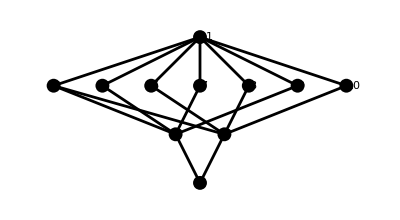

```mathematica
(* Example 6.16 *)A = {{0,s,0,0,0,t},{s,0,t,0,0,0},{0,t,0,s,0,0},{0,0,s,0,t,0},{0,0,0,t,0,s},{t,0,0,0,s,0}};
MatrixForm[A]
computeLattice[A/.{s -> 1, t -> 2}]
```

Here the equivalence classes are {5, 7, 9} and {6, 8, 10}

Compute (0 | 0 | 0
0 | 1 | -1
0 | -1 | 1)-invariant polydiagonal subspaces.

The color vectors of the invariant polydiagonal subspaces are

1 | 0 | 0 | 0
2 | 0 | 1 | -1
3 | 0 | 1 | 1
4 | 1 | -1 | -1
5 | 1 | 0 | 0
6 | 1 | 1 | 1
7 | 0 | 1 | 2
8 | 1 | 2 | -2
9 | 1 | 2 | 2
10 | 1 | 2 | 3

The ordering of subspaces W<=V iff W subseteq V is

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 7 | 8 | 10 |  |  |  |  |  | 
3 | 7 | 9 | 10 |  |  |  |  |  | 
4 | 9 | 10 |  |  |  |  |  |  | 
5 | 8 | 9 | 10 |  |  |  |  |  | 
6 | 9 | 10 |  |  |  |  |  |  | 
7 | 10 |  |  |  |  |  |  |  | 
8 | 10 |  |  |  |  |  |  |  | 
9 | 10 |  |  |  |  |  |  |  | 
10 |  |  |  |  |  |  |  |  |

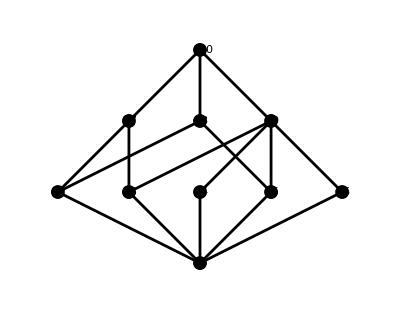

```mathematica
(* Example 6.19 *)
L = {{0,0,0},{0,1,-1},{0, -1,1}};
computeLattice[L]
```